LLs diagram for Dirac system

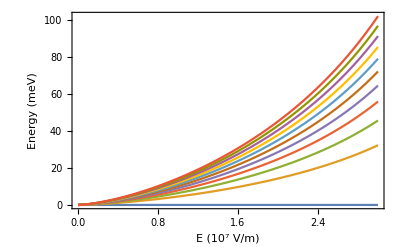

```mathematica
Clear[e,me,m,k,A1,h,n1,q,a,p]
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.191;
a=120*10^-9;
f=1*y*10^7(*E field*);
VY2=(v^2*f^2*h^2)/ω^2(*e^2V^2*);
VN=(1-VY2/ω^2);
Bfield=(VY2*f*2*Pi*h)/(4*ω^3*a*VN);
Clear[w,y];
w[n_]:=(10^3*√(n*((2*v^2*Bfield*h)/VN))); (*m^2e^2V^2s^2/s^2m^2=*)
Plot [{w[0],w[1],w[2],w[3],w[4],w[5],w[6],w[7],w[8],w[9],w[10]}, {y,0,3}, Frame-> True,FrameLabel->{"E (10^7 V/m)","Energy (meV)","",""} ]
```

```mathematica
(For graphene parameters, light energy 191mev , period 120 nm, and electric field 1-3*10^7 V/m)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.191;
a=120*10^-9;
f=2*10^7(*E field*)
Energy=(1*v*f*h)/ω;
ω/2;
V2=(v^2*f^2*h^2)/ω^2;
Bfield=(V2*h*f*2*Pi)/(4*ω^3*a*(1-V2/ω^2))
phi0=f/ω*(1*10^-9) (*we need to fix a and energy unit of light frequency*)
```

20000000

0.134923

0.104712

LLs for 2 DEG systems ... ... ... ... with same period and frequency as above

Set::write: Tag Times in energy field magnetic is Protected.

Set::write: Tag Times in 6.5534×10^11 (3.14924×10^-19 y^4) is Protected.

Set::write: Tag Times in 1.6×10^-19 4.09588×10^30 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

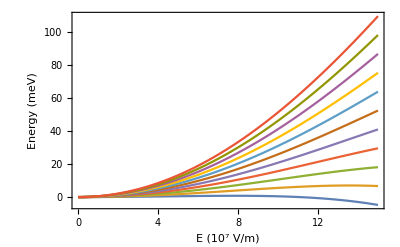

```mathematica
Clear[e,me,m,k,A1,h,n1,q,a,p]
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.191;
a=120*10^-9;
f=1*y*10^7(*E field*);
V1=(f^2*h^2)/ω^2; (*e^2V^2s^2/m^2*)
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2); (*e^2V^2s^2/m^2*s/m^2kg=eVs/m^2*)
magnetic field energy =(h*e*Bfield)/m; (*eVs/kg*eVs/m^2=eV*)
(e/(4*m))*((e*V1*h*2*Pi)/(m*ω*a))^2=U^2/4m; (*{e^2V^2s^2/m^2*s/mkg}^2={e^2V^2s^2/m^2*s/mkg}^2={eVs/m}^2*)
(e/(4*m))=(e/(4*m)); (*e^2V^2s^2/m^2kg=eV*)
Clear[w,y];
w[n_]:=(10^3*((n+1/2)*((h*e*Bfield)/m)-(e/(4*m))*((e*V1*h*2*Pi)/(m*ω*a))^2)); (*eVs*e*Vs/m^2*kg, where joule=kgm^2/s^2*)
Plot [{w[0],w[1],w[2],w[3],w[4],w[5],w[6],w[7],w[8],w[9],w[10]}, {y,0,15}, Frame-> True,FrameLabel->{"E (10^7 V/m)","Energy (meV)","",""} ]
```

```mathematica
(for spatial period of 100 nm and frquency 191 meV and field 5*10^7 V/m)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.191;
a=100*10^-9;
f=2*10^7(*E field*);
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

0.169248

```mathematica
reducing the period to 10 nm
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.191;
a=10*10^-9;
f=5*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

50000000

105.78

```mathematica
for increasing electric field
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.191;
a=100*10^-9;
f=20*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

200000000

16.9248

```mathematica
increasing or decreasing frequency
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.120;
a=100*10^-9;
f=5*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

50000000

4.26541

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.190;
a=100*10^-9;
f=4.8*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

4.8×10^7

0.990344

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.191;
a=10*10^-9;
f=5*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

50000000

105.78

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
me=9.11*10^-31;
m=0.067*me;
ω=0.190;
a=10*10^-9;
f=5*10^7(*E field*)
Energy=(1*v*f*h)/ω;
V1=(f^2*h^2)/ω^2;
Bfield=(e*V1*h*4*Pi^2)/(m*ω*a^2)
```

50000000

107.459

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=(0.139*ω)/(h*v);
Energy=(1*v*f*h)/ω;
ω/2;
UU=(1*v*f*h)/ω^2*1.4;
UU=((1*v*f*h)/ω^2)^2;
a=√((h*UU*4*Pi^2)/(1*(1-UU)))
```

1.72952×10^-7

which means 
we have a = 200nm

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=(0.139*ω)/(h*v);
Energy=(1*v*f*h)/ω;
ω/2;
UU=(1*v*f*h)/ω^2*1.4;
UU=((1*v*f*h)/ω^2)^2;
a=√((h*UU*4*Pi^2)/(5*(1-UU)))
```

7.73463×10^-8

which means 
we have a = 80nm

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=(0.139*ω)/(h*v);
Energy=(1*v*f*h)/ω;
ω/2;
UU=(1*v*f*h)/ω^2*1.4;
UU=((1*v*f*h)/ω^2)^2;
a=√((h*UU*4*Pi^2)/(10*(1-UU)))
```

5.46921×10^-8

```mathematica
(*For TIs , we have energy 0.120eV. and U0 in my case is*)
e=1.6*10^(-19);
h=6.58*10^(-16);
V1=(3*10^-10)/h;
ω=0.120;
ω/h;
f=(0.062*ω)/(h*V1)
VV=(1*V1*f*h)/ω^2
UU2=((1*V1*f*h)/ω^2)^2
```

2.48×10^7

0.516667

0.266944

```mathematica
(*For graphene , we have energy 0.190eV. and U0 in my case is*)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=(0.139*ω)/(h*v)
Energy=(1*v*f*h)/ω;
ω/2;
UU=(1*v*f*h)/ω^2*1.4
UU=((1*v*f*h)/ω^2)^2;
```

4.01368×10^7

1.02421

```mathematica
(*science paper photon energy of 120meV and gap of 62meV, velocity 3eVA, with electric field 2.4 or 2.5*)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
V1=(3*10^-10)/h;
v=V1;
ω=0.120;
f=2*2.5*10^7;
ω/h
gap=(v^2*f^2)/(ω^3/h^2)
```

1.82371×10^14

0.130208

```mathematica
(*Flat band condition for above TIs science paper*)
e=1.6*10^(-19);
h=6.58*10^(-16);
V1=(3*10^-10)/h;
v=V1;
ω=0.120;
f=5*10^7;
ω/h;
gap2=(v^2*f^2)/(ω^2/h^2)*(1/ω^2)
```

1.08507

```mathematica
(*graphene paper photon energy and gap 70meV and 46 THz*)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=1  *2.4*10^7;
ω/h;
gap1=(v^2*f^2)/(ω^3/h^2)
gap3=((v^2*f^2)/(ω^3/h^2))^2
gap2nd=(v^2*f^2)/(ω^3/h^2)*(1/ω)
gap4th=((v^2*f^2)/(ω^3/h^2)*(1/ω))^2
```

0.0363591

0.00132199

0.191364

0.0366201

```mathematica
(*my second order term for flat band*)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=5.5*10^7;
ω/h;
gap2=(v^2*f^2)/(ω^2/h^2)*(1/ω^2)
```

1.00499

```mathematica
(*gap at flat band condition*)
```

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
v=1*10^6;
ω=0.190;
f=5.5*10^7;
ω/h;
gap3=(v^2*f^2)/(ω^3/h^2)
```

0.190949

```mathematica
e=1.6*10^(-19);
h=6.58*10^(-16);
V1=(3*10^-10)/h;
v=V1;
ω=0.120;
f=2.2*10^7;
ω/h;
gap3=(v^2*f^2)/(ω^3/h^2)
```

0.0252083

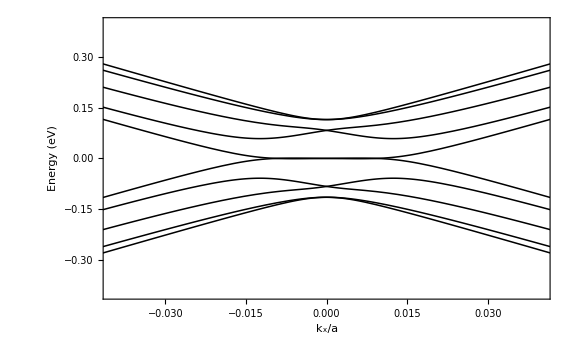

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=50*10^-9;
a2=50*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
ky=0;
B=10;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot[Sort[Eigenvalues[M]],{kx,-0.05,0.05},PlotRange->{{-0.04,0.04},{-0.4,0.4}},Frame-> True,LabelStyle->Directive[20],FrameStyle->{GrayLevel[0],Thickness[0.002]},PlotStyle->{{AbsoluteThickness[1.1],GrayLevel[0]}},FrameLabel->{"k_x/a","Energy (eV)","",""} ]
```

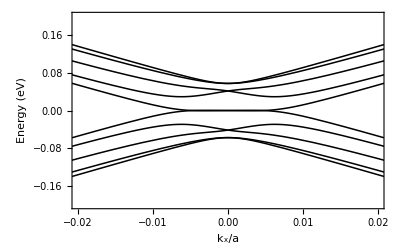

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=100*10^-9;
a2=100*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
ky=0;
B=2.5;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot[Sort[Eigenvalues[M]],{kx,-0.05,0.05},PlotRange->{{-0.02,0.02},{-0.2,0.2}},Frame-> True,LabelStyle->Directive[20],FrameStyle->{GrayLevel[0],Thickness[0.002]},PlotStyle->{{AbsoluteThickness[1.1],GrayLevel[0]}},FrameLabel->{"k_x/a","Energy (eV)","",""} ]
```

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=20*10^-9;
a2=20*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
B=65.04;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot3D[Sort[Eigenvalues[M]][[5;;6]],{kx,-0.03,0.03},{ky,-0.02,0.02},PlotRange->All,BoxRatios->{1,1,1},LabelStyle->Directive[20],AxesLabel->{kx,ky,  Energy  (eV)}]
```

-Graphics3D-

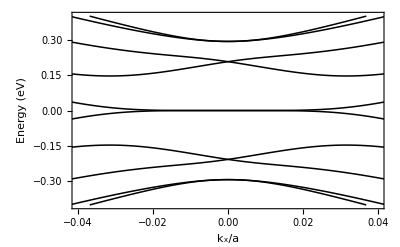

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=20*10^-9;
a2=20*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
ky=0;
B=65.04;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot[Sort[Eigenvalues[M]],{kx,-0.05,0.05},PlotRange->{{-0.04,0.04},{-0.4,0.4}},Frame-> True,LabelStyle->Directive[20],FrameStyle->{GrayLevel[0],Thickness[0.002]},PlotStyle->{{AbsoluteThickness[1.1],GrayLevel[0]}},FrameLabel->{"k_x/a","Energy (eV)","",""} ]
```

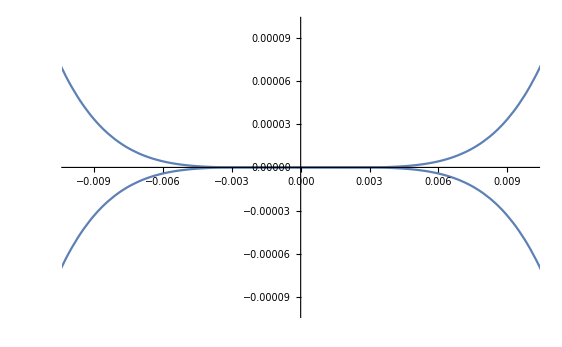

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=20*10^-9;
a2=20*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
ky=0;
B=65.04;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot[Sort[Eigenvalues[M]],{kx,-0.05,0.05},PlotRange->{{-0.01,0.01},{-0.0001,0.0001}}]
```

```mathematica
Clear[e,h,a,B,a1,a2,v,ω,y,k,k1,k2,kx,ky,y]
e=1.6*10^(-19);
h=6.59*10^(-16);
a=1.42*10^-10;
a1=20*10^-9;
a2=20*10^-9;
v=1*10^6;
(v*h*π)/a;
ω=v*h;
B=65.04;
Vx=(v*B*a1)/(2*π);
Vy=(v*B*a2)/(2*π);
y=1;
k1=(v*h*2*π)/a1;
k2=(v*h*2*π)/a2;
M={{0,ω*(kx-I*ky)/(a),0,-0.5*Vx,0,0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy},{ω*(kx+I*ky)/(a),0,0.5*Vx,0,-0.5*Vx,0,-I*y*.5*Vy,0,I*y*.5*Vy,0},{0,0.5*Vx,0,ω*(kx-I*ky)/(a)+k1,0,0,0,0,0,0},{-0.5*Vx,0,ω*(kx+I*ky)/(a)+k1,0,0,0,0,0,0,0},{0,-0.5*Vx,0,0,0,ω*(kx-I*ky)/(a)-k1,0,0,0,0},{0.5*Vx,0,0,0,ω*(kx+I*ky)/(a)-k1,0,0,0,0,0},{0,I*0.5*Vy,0,0,0,0,0,ω*(kx-I*ky)/(a)-I*k2,0,0},{I*0.5*Vy,0,0,0,0,0,ω*(kx+I*ky)/(a)+I*k2,0,0,0},{0,-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx-I*ky)/(a)+I*k2},{-I*y*0.5*Vy,0,0,0,0,0,0,0,ω*(kx+I*ky)/(a)-I*k2,0}};
M//MatrixForm;
Plot3D[Sort[Eigenvalues[M]],{kx,-0.05,0.05},{ky,-0.05,0.05},PlotRange->{{-0.01,0.01},{-0.0001,0.0001}}]
```

-Graphics3D-